# Tanabe - Sugano Diagrams ~E(ζ/B, C/B, Dq/B) ~ --------------------------------------

The multiplet structure of an ion subject to a crystal field with octahedral symmetry is determined by the strength Dq of the crystal field,  the values for the Racah parameters B and C,and the strength of the spin-orbit coupling ζ.  This notebook uses precomputed values to this function to show the effects that varying each parameter has. It can also query Hartree-Fock values for B,C, and ζ to estimate the multiplet structure of all transition metal ions.

-Graphics-

The section E(ζ/B, C/B, Dq/B) shows these data in abstract with sliders that corresponds to the three ratios: ζ/B, C/B and Dq/B.
The section Transition Metal Ions queries the estimated values for the provided ion and shows the accompanying multiplet structure as a function of the strength of the crystal field. In here the colors indicate the multiplicity of the shown states.

ATTENTION: This notebook requires a large file (2.9 GB) of pre-computed values that is not available on the online repository. 
This file (tsk_hypercube_int16.h5.gz) can be downloaded from Google Drive at this link.

```mathematica
AppendTo[$Path,NotebookDirectory[]];
Get["TS_diag.m"]
```

## E(ζ/B, C/B, Dq/B)

Here one may see the energies of the different eigenstates under a crystal field with octahedral symmetry as a function of ζ/B, C/B, Dq/B.

### Without multiplicities

```mathematica
Manipulate[(
γoB=Nearest[γsoB,γ][[1]];
ζoB=Nearest[ζsoB,ζ][[1]];
γidx=Position[γsoB,γoB][[1,1]]-1;
ζidx=Position[ζsoB,ζoB][[1,1]]-1;
key=keyTemplate[<|"num_electrons"->numElectrons,"gamma_idx"->γidx,"zeta_idx"->ζidx|>];
data=Import[h5fname,key]/normalizer;
minima=Min/@data;
data=data-minima;
data=Transpose[data];
data=Transpose[{DqsoB,#}]&/@data;
ListPlot[data,
Frame->True,
FrameLabel->{"Dq/B","E/B"},
FrameStyle->Directive[16],
ImageSize->800,
Joined->joined,
PlotStyle->Directive[Thick,Blue],
PlotRange->{{-6,6},{0,Erange}}
]
),
Row[{Column[{
Control[{{Erange,50},1,399,1}],
Control[{{ζ,0},0,Max[ζsoB],0.01}],
Control[{{γ,4.},Min[γsoB],Max[γsoB],0.01}],
Control[{{numElectrons,2},{1,2,3,4,5,6,7,8,9},ControlType->SetterBar}],
Control[{{joined,True},{True,False}}]
}]}],
TrackedSymbols:>True]
```

### With multiplicities

```mathematica
Manipulate[(
γoB=Nearest[γsoB,γ][[1]];
ζoB=Nearest[ζsoB,ζ][[1]];
γidx=Position[γsoB,γoB][[1,1]]-1;
ζidx=Position[ζsoB,ζoB][[1,1]]-1;
key=keyTemplate[<|"num_electrons"->numElectrons,"gamma_idx"->γidx,"zeta_idx"->ζidx|>];
data=Import[h5fname,key]/normalizer;
minima=Min/@data;
data=data-minima;
data=Transpose[data];
data=Transpose[{DqsoB,#}]&/@data;
tdata=Transpose[data];
multidata=Association[];
multidata=Table[
(Dq=datum[[1,1]];
eivals=Chop[Last/@datum];
eivals=Round[eivals,0.001];
uniqueEigenvals=DeleteDuplicates[eivals];
Table[{Dq,eival,Count[eivals,eival]},{eival,uniqueEigenvals}]
)
,{datum,tdata}];
multidata=Flatten[multidata,1];
multis=Sort[DeleteDuplicates[Last/@multidata]];
data=Table[{#[[1]],#[[2]]}&/@Select[multidata,#[[3]]==count&],{count,multis}];
ListPlot[data,
Frame->True,
FrameLabel->{"Dq/B","E/B"},
ImageSize->1300,
AspectRatio->1/2,
PlotStyle->Automatic,
PlotLegends->multis,
FrameStyle->Directive[16,Thick],
PlotLabel->Row[{Superscript["d",numElectrons]," | ζ/B = ",ζoB," | C/B = ",γoB},BaseStyle->"Title"],
PlotRange->{{-Dqrange,Dqrange},{-0.5,Erange}}
]
),
Row[{Spacer[400],
Column[{
Style["Multiplet Structure of d^n Ions in a Cubic Field",20,Underlined],
"",
Row[{
Control[{{Erange,50,Style["E/B range",15]},1,399,1}],
Spacer[10],
Control[{{Dqrange,4.,Style["Dq/B range",15]},1,6,0.1}]
}],
Row[{
Control[{{γ,4.4,Style["C/B",15]},Min[γsoB],Max[γsoB],0.01}],
Spacer[10],
Control[{{ζ,0,Style["ζ/B",15]},0,Max[ζsoB],0.01}]
}
],
Control[{{numElectrons,2,Style["d^n",15]},{1,2,3,4,5,6,7,8,9},ControlType->SetterBar}],
Spacer[10]
},Alignment->Center]
}
],
TrackedSymbols:>True]
```

```mathematica
figTemplate=StringTemplate["/Users/juan/Temp/figs/`numElectrons`-`idx0`-`idx1`.jpg"];
figs=ParallelDo[
(
γidx=Position[γsoB,γoB][[1,1]]-1;
ζidx=Position[ζsoB,ζoB][[1,1]]-1;
key=keyTemplate[<|"num_electrons"->numElectrons,"gamma_idx"->γidx,"zeta_idx"->ζidx|>];
data=Import[h5fname,key]/normalizer;
minima=Min/@data;
data=data-minima;
data=Transpose[data];
data=Transpose[{DqsoB,#}]&/@data;
tdata=Transpose[data];
multidata=Association[];
multidata=Table[
(Dq=datum[[1,1]];
eivals=Chop[Last/@datum];
eivals=Round[eivals,0.001];
uniqueEigenvals=DeleteDuplicates[eivals];
Table[{Dq,eival,Count[eivals,eival]},{eival,uniqueEigenvals}]
)
,{datum,tdata}];
multidata=Flatten[multidata,1];
multis=Sort[DeleteDuplicates[Last/@multidata]];
data=Table[{#[[1]],#[[2]]}&/@Select[multidata,#[[3]]==count&],{count,multis}];
fig=ListPlot[data,
Frame->True,
FrameLabel->{"Dq/B","E/B"},
ImageSize->1300,
AspectRatio->1/2,
PlotStyle->Automatic,
PlotLegends->multis,
FrameStyle->Directive[16,Thick],
PlotLabel->Row[{Superscript["d",numElectrons]," | ζ/B = ",ζoB," | C/B = ",γoB},BaseStyle->"Title"],
PlotRange->{{-4,4},{-0.5,50}}
];
 figFname=figTemplate[<|"numElectrons"->numElectrons,"idx0"->γidx,"idx1"->ζidx|>];
Export[figFname,fig];
),{numElectrons,{1,2,3,4,5,6,7,8,9}},{γoB,γsoB[[;;;;5]]},{ζoB,ζsoB[[;;;;5]]}];
```

```mathematica
Length[figs]
```

## Transition Metal Ions

Taking the HF values for free ions, here one may view an approximation of their energy levels under a crystal field with octahedral symmetry.

### With Multiplicity

```mathematica
Manipulate[(
TSKDiagram[nephRatio,Erange,DqrangeR,shell,atom,charge,vLine,DqLine,positiveOnly,p]
),
Row[{Spacer[200],
Column[{
Control[{{nephRatio,1,"β=B_real/B_HF"},0.1,1,0.01}],
Control[{{Erange,4,"Erange"},0.1,5,0.1}],
Control[{{DqrangeR,1,"Dqrange"},0.1,2,0.1}] 
}],
Column[{
Control[{{shell,"3d"},{"3d","4d","5d"}}],
Control[{{atom,"Cu"},shellToatoms[shell],ControlType->SetterBar}],
Control[{{charge,4},{2,3,4,5,6,7},ControlType->RadioButton}]
}],
Column[{Control[{{vLine,1},0,6}],
Control[{{DqLine,0.1},-2,2}],
Control[{{positiveOnly,False},{True,False}}],
Control[{{p,{0.5,0.5}},ControlType->Locator}]
}]
}],
TrackedSymbols:>True
]
```

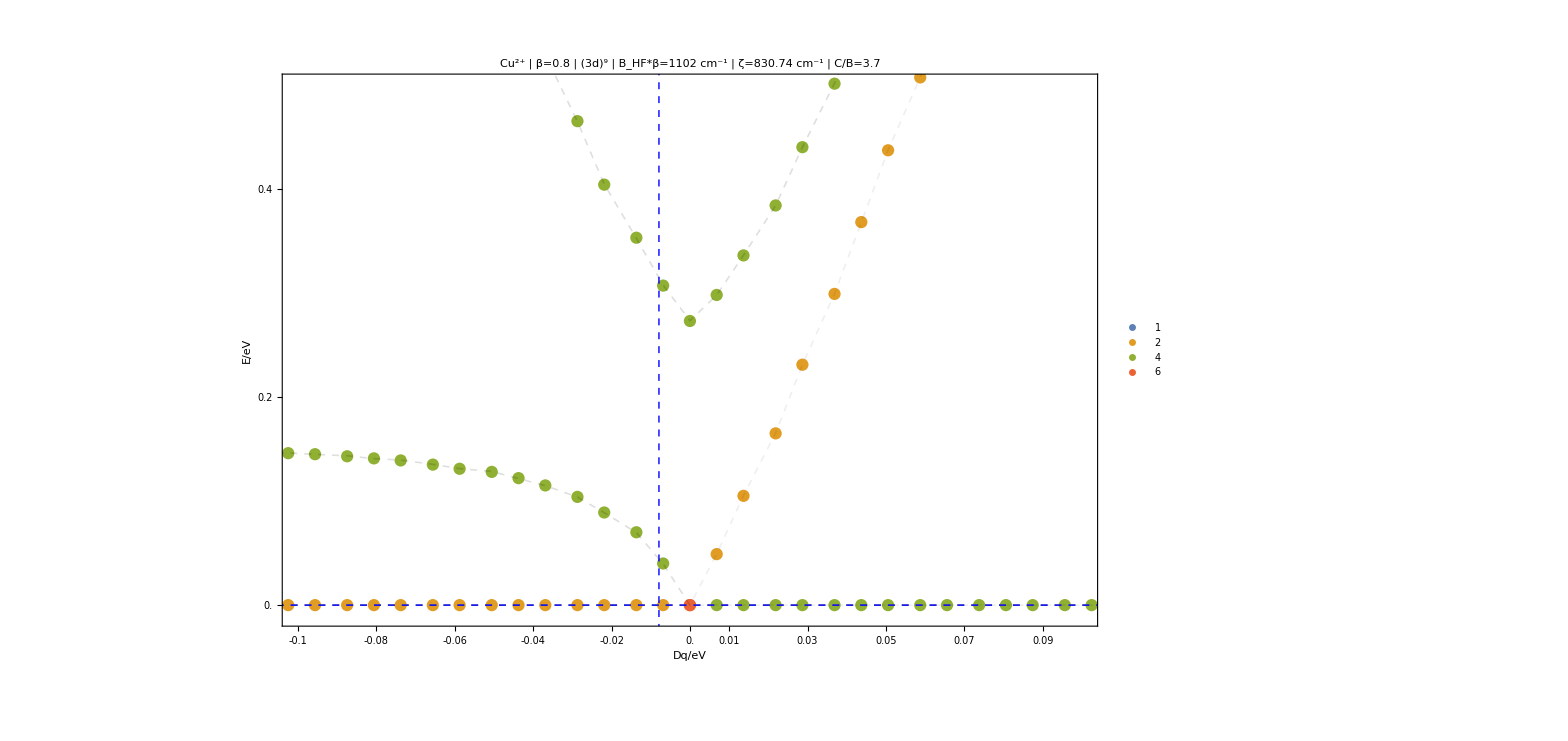

```mathematica
Show[TSKDiagram[0.8,0.5,0.1,"3d","Cu",2,0,-0.0079,False],PlotRange->{{-0.1,0.1},{-.01,0.5}},Background->White]
```

### Without Multiplicity

```mathematica
allMinima=Association[];
Manipulate[(
key={atom,charge};
If[
MemberQ[Keys[cowanA],key],
(
γ=cowanA[key]["C/B"];
B=Round[cowanA[key]["B"],1];
ζ=cowanA[key]["ζ"];
ζ=ζ/B;
γoB=Nearest[γsoB,γ][[1]];
ζoB=Nearest[ζsoB,ζ][[1]];
γidx=Position[γsoB,γoB][[1,1]]-1;
ζidx=Position[ζsoB,ζoB][[1,1]]-1;
numElectrons=cowanA[key]["d^n"];
tskkey=keyTemplate[<|"num_electrons"->numElectrons,"gamma_idx"->γidx,"zeta_idx"->ζidx|>];
If[MemberQ[tskkeys,tskkey],(
data=Import[h5fname,tskkey]/normalizer;
If[KeyExistsQ[allMinima,tskkey],
minima=allMinima[tskkey];
,
(minima=Min/@data;
allMinima[tskkey]=minima;)
];

data=data-minima;
data=Transpose[data];
data=Transpose[{DqsoB*B/evtocm,#*B/evtocm}]&/@data;
xTicks=Table[{ee/B*evtocm*B/evtocm,ee},{ee,-Round[6/B*evtocm,0.1],Round[6/B*evtocm,0.1],0.1}];
yTicks=Table[{ee/B*evtocm*B/evtocm,ee*B/evtocm},{ee,0,Round[10/B*evtocm,0.25],0.25}];
{γoB,ζoB};
plotLabel=Row[{Superscript[atom,ToString[charge]<>"+"]," | ",Superscript[shell,numElectrons]," | B="<>ToString[B]<>"cm^-1", " | ζ="<>ToString[ζ*B]<>"cm^-1"," | C/B="<>ToString[γoB] },BaseStyle->"Title"];
ListPlot[data,
Frame->{{True,True},{True,True}},
FrameLabel->{"Dq/eV","E/eV"},
FrameStyle->Directive[16],
ImageSize->1200,
Joined->joined,
PlotStyle->Directive[Thick,Blue],
(*FrameTicks->{{yTicks,None},{xTicks,None}},*)
PlotRange->{{-Dqrange,Dqrange},{0,Erange*evtocm/B*B/evtocm}},
PlotLabel->plotLabel,
Epilog->{{Thickness[.005],Blue,Line[{{-6*B/evtocm,0},{6*B/evtocm,0}}]},
{Red,Dashed,Line[{{-6*B/evtocm,vLine*evtocm/B*B/evtocm},{6*B/evtocm,vLine*evtocm/B*B/evtocm}}]},
{Red,Dashed,Line[{{DqLine,0},{DqLine,Erange}}]},
{Gray,Dashed,Line[{{-6*B/evtocm,0.025},{6*B/evtocm,0.025}}]}
}
]),
"MissingB"
]
),
"MissingA"
]
),
Row[{Spacer[400],
Column[{
Control[{{Erange,2},0.1,5,0.1}],
Control[{{Dqrange,1},0.1,2,0.1}],
Control[{{joined,True},{True,False}}]
}],
Column[{Control[{{shell,"3d"},{"3d","4d","5d"}}],
Control[{{atom,"Cu"},shellToatoms[shell],ControlType->SetterBar}],
Control[{{charge,4},{2,3,4,5,6,7},ControlType->RadioButton}]
}],
Column[{Control[{{vLine,1},0,6}],
Control[{{DqLine,0.1},0,2}]}]
}],
TrackedSymbols:>True
]
```